## Open System Plots

```mathematica
SetDirectory["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0_Neel/L10"];
```

```mathematica
tListClosed = ToExpression[#]&/@(Import["tList_L_10_alpha_0.0000_w_0.01_R_200.txt","Table"]//Flatten);
KCW0pt01Closed = Import["complexity_L_10_alpha_0.0000_w_0.01_R_200.txt","Table"]//Flatten;
KCW0pt1Closed = Import["complexity_L_10_alpha_0.0000_w_0.1_R_200.txt","Table"]//Flatten;
KCW1Closed = Import["complexity_L_10_alpha_0.0000_w_1._R_200.txt","Table"]//Flatten;
KCW6pt5Closed = Import["complexity_L_10_alpha_0.0000_w_6.5_R_200.txt","Table"]//Flatten;

KIPRW0pt01Closed = Import["KIPR_L_10_alpha_0.0000_w_0.01_R_200.txt","Table"]//Flatten;
KIPRW0pt1Closed = Import["KIPR_L_10_alpha_0.0000_w_0.1_R_200.txt","Table"]//Flatten;
KIPRW1Closed = Import["KIPR_L_10_alpha_0.0000_w_1._R_200.txt","Table"]//Flatten;
KIPRW6pt5Closed = Import["KIPR_L_10_alpha_0.0000_w_6.5_R_200.txt","Table"]//Flatten;
```

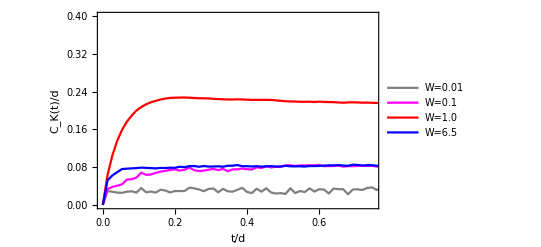

```mathematica
Show[ListLinePlot[{Transpose[{tListClosed,KCW0pt01Closed}],Transpose[{tListClosed,KCW0pt1Closed}],Transpose[{tListClosed,KCW1Closed}],Transpose[{tListClosed,KCW6pt5Closed}]},PlotLegends->{"W=0.01","W=0.1","W=1.0","W=6.5"},PlotRange->{{0,0.75},{0,0.4}},PlotStyle->{Gray,Magenta,Red,Blue}],Frame->True,LabelStyle->Directive[Bold, Black,12],FrameLabel->{Style["t/d",Bold,Black,14],Style["C_K(t)/d",Bold,Black,14]}]
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/KC_closed_alpha_0_L10_R200.pdf",%]
```

/Users/aneekphys/Documents/MBL1 plots/KC_closed_alpha_0_L10_R200.pdf

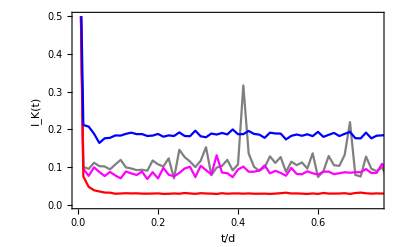

```mathematica
Show[ListLinePlot[{Transpose[{tListClosed,KIPRW0pt01Closed}],Transpose[{tListClosed,KIPRW0pt1Closed}],Transpose[{tListClosed,KIPRW1Closed}],Transpose[{tListClosed,KIPRW6pt5Closed}]},PlotRange->{{0,0.75},{0,0.5}},PlotStyle->{Gray,Magenta,Red,Blue}],Frame->True,LabelStyle->Directive[Bold, Black,14],FrameLabel->{Style["t/d",Bold,Black,16],Style["I_K(t)",Bold,Black,16]}]
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/KIPR_closed_alpha_0_L10_R200.pdf",%]
```

/Users/aneekphys/Documents/MBL1 plots/KIPR_closed_alpha_0_L10_R200.pdf

## α=5 x 10^-3

```mathematica
SetDirectory["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.005_Neel/L10"];
```

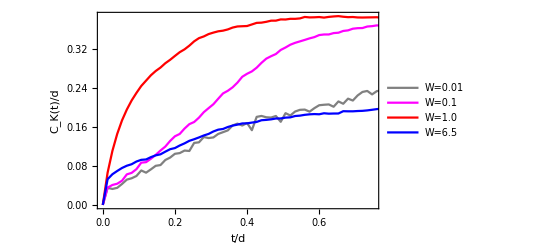

```mathematica
tListOpen = ToExpression[#]&/@(Import["tList_L_10_alpha_0.005_w_0.01_R_200.txt","Table"]//Flatten);
KCW0pt01Open = Import["complexity_L_10_alpha_0.005_w_0.01_R_200.txt","Table"]//Flatten;
KCW0pt1Open = Import["complexity_L_10_alpha_0.005_w_0.1_R_200.txt","Table"]//Flatten;
KCW1Open= Import["complexity_L_10_alpha_0.005_w_1._R_200.txt","Table"]//Flatten;
KCW6pt5Open= Import["complexity_L_10_alpha_0.005_w_6.5_R_200.txt","Table"]//Flatten;

KIPRW0pt01Open = Import["KIPR_L_10_alpha_0.005_w_0.01_R_200.txt","Table"]//Flatten;
KIPRW0pt1Open = Import["KIPR_L_10_alpha_0.005_w_0.1_R_200.txt","Table"]//Flatten;
KIPRW1Open= Import["KIPR_L_10_alpha_0.005_w_1._R_200.txt","Table"]//Flatten;
KIPRW6pt5Open= Import["KIPR_L_10_alpha_0.005_w_6.5_R_200.txt","Table"]//Flatten;

Show[ListLinePlot[{Transpose[{tListOpen,KCW0pt01Open}],Transpose[{tListOpen,KCW0pt1Open}],Transpose[{tListOpen,KCW1Open}],Transpose[{tListOpen,KCW6pt5Open}]},PlotLegends->{"W=0.01","W=0.1","W=1.0","W=6.5"},PlotRange->{{0,0.75},Automatic},PlotStyle->{Gray,Magenta,Red,Blue}],Frame->True,LabelStyle->Directive[Bold, Black,12],FrameLabel->{Style["t/d",Bold,Black,14],Style["C_K(t)/d",Bold,Black,14]}]
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/KC_open_alpha_0.005_L10_R200.pdf",%]
```

/Users/aneekphys/Documents/MBL1 plots/KC_open_alpha_0.005_L10_R200.pdf

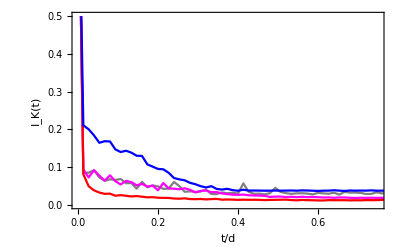

```mathematica
Show[ListLinePlot[{Transpose[{tListOpen,KIPRW0pt01Open}],Transpose[{tListOpen,KIPRW0pt1Open}],Transpose[{tListOpen,KIPRW1Open}],Transpose[{tListOpen,KIPRW6pt5Open}]},PlotRange->{{0,0.75},{0,0.5}},PlotStyle->{Gray,Magenta,Red,Blue}],Frame->True,LabelStyle->Directive[Bold, Black,14],FrameLabel->{Style["t/d",Bold,Black,16],Style["I_K(t)",Bold,Black,16]}]
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/KIPR_open_alpha_0.005_L10_R200.pdf",%]
```

/Users/aneekphys/Documents/MBL1 plots/KIPR_open_alpha_0.005_L10_R200.pdf

```mathematica
SetDirectory["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_alpha_0.005_Neel/L10verylate"];
```

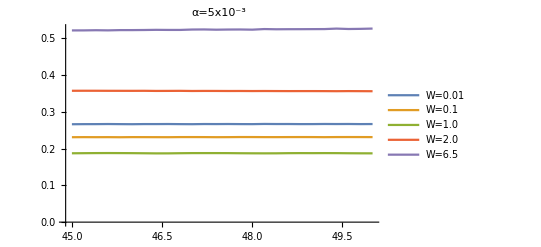

```mathematica
tListOpenvl = ToExpression[#]&/@(Import["tList_L_10_alpha_0.005_w_0.01_R_200.txt","Table"]//Flatten);
KCW0pt01Openvl = Import["complexity_L_10_alpha_0.005_w_0.01_R_200.txt","Table"]//Flatten;
KCW0pt1Openvl = Import["complexity_L_10_alpha_0.005_w_0.1_R_200.txt","Table"]//Flatten;
KCW1Openvl= Import["complexity_L_10_alpha_0.005_w_1._R_200.txt","Table"]//Flatten;
KCW2Openvl= Import["complexity_L_10_alpha_0.005_w_2._R_200.txt","Table"]//Flatten;
KCW6pt5Openvl= Import["complexity_L_10_alpha_0.005_w_6.5_R_200.txt","Table"]//Flatten;

KIPRW0pt01Openvl = Import["KIPR_L_10_alpha_0.005_w_0.01_R_200.txt","Table"]//Flatten;
KIPRW0pt1Openvl = Import["KIPR_L_10_alpha_0.005_w_0.1_R_200.txt","Table"]//Flatten;
KIPRW1Openvl= Import["KIPR_L_10_alpha_0.005_w_1._R_200.txt","Table"]//Flatten;
KIPRW2Openvl= Import["KIPR_L_10_alpha_0.005_w_2._R_200.txt","Table"]//Flatten;
KIPRW6pt5Openvl= Import["KIPR_L_10_alpha_0.005_w_6.5_R_200.txt","Table"]//Flatten;

ListLinePlot[{Transpose[{tListOpenvl,KCW0pt01Openvl}],Transpose[{tListOpenvl,KCW0pt1Openvl}],Transpose[{tListOpenvl,KCW1Openvl}],Transpose[{tListOpenvl,KCW2Openvl}],Transpose[{tListOpenvl,KCW6pt5Openvl}]},PlotLegends->{"W=0.01","W=0.1","W=1.0","W=2.0","W=6.5"},PlotLabel->"α=5x10^-3"]
```

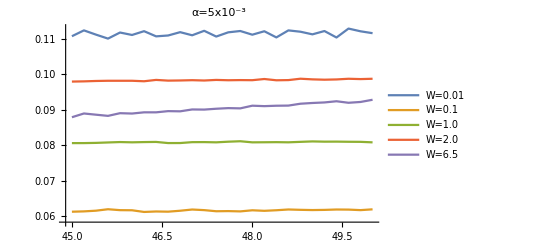

```mathematica
ListLinePlot[{Transpose[{tListOpenvl,KIPRW0pt01Openvl}],Transpose[{tListOpenvl,KIPRW0pt1Openvl}],Transpose[{tListOpenvl,KIPRW1Openvl}],Transpose[{tListOpenvl,KIPRW2Openvl}],Transpose[{tListOpenvl,KIPRW6pt5Openvl}]},PlotLegends->{"W=0.01","W=0.1","W=1.0","W=2.0","W=6.5"},PlotLabel->"α=5x10^-3"]
```

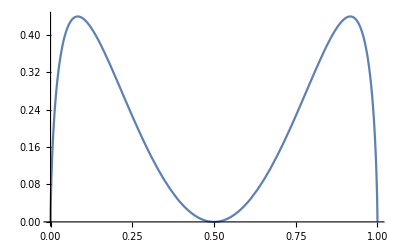

```mathematica
Plot[k(1-k)Log[(1-k)/k]^2,{k,0.000001,0.999995}]
```